## Metropolitan Play station

```mathematica
vertAndEdges[fileName_]:=Module[{str,v={},e={},rules},
str=ReadString[fileName];
rules:={"v"~~Whitespace~~x:NumberString~~Whitespace~~NumberString~~Whitespace~~z:NumberString:>AppendTo[v,{ToExpression[x],ToExpression[z]}],
"e"~~Whitespace~~e1:NumberString~~Whitespace~~e2:NumberString:>AppendTo[e,{ToExpression[e1],ToExpression[e2]}]};
StringCases[str,rules];
{v,e}];
indexEdgeToLine[v_,e_]:=Module[{takeV,takeL},
takeV[idx_]:=Part[v,idx+1];
takeL[{x_,y_}]:={takeV[x],takeV[y]};
takeL/@e];
getRegionLines[v_,e_,cric_]:=Module[
{takeV,takeL,availE,availV,selectedV,selectedE,ruleE,ruleV},
takeV[idx_]:=Part[v,idx+1];
takeL[{x_,y_}]:={takeV[x],takeV[y]};
ruleE[line_]:=And@@Flatten@cric@@@takeL[line];
ruleV[old_,{new_}]:=old:>new-1;
availE=Select[e,ruleE];
Assert[Length[availE]>0];
availV=DeleteDuplicates@Flatten@availE;
selectedV=Part[v,#+1& /@availV];
selectedE=Replace[availE,MapIndexed[ruleV,availV],{2}];
{selectedV,selectedE}]
showGraph:=Graphics[#,ImageSize->Large]&@*Line@*indexEdgeToLine;
```

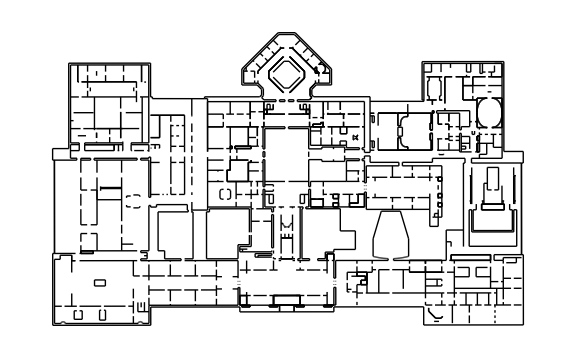

```mathematica
{v,e}=vertAndEdges["C:\\Users\\kaidonghu\\Desktop\\met2_init.graph"];
showGraph[v,e]
```

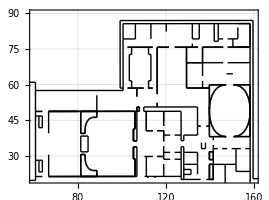

```mathematica
Graphics[Line@indexEdgeToLine[v,e],PlotRange->{{60,160},{20,90}},
GridLines->Automatic,Frame->True,GridLinesStyle->Directive[Gray, Dashed]]
```

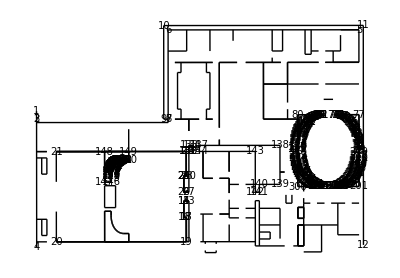

```mathematica
{v1,e1}=getRegionLines[v,e,(160>#1>60&&#2>18)&];
Graphics[{
Line@indexEdgeToLine[v1,e1],
MapIndexed[Text[Style[First@#2,FontSize->10],#1]&,v1]
}]
```

## Argumented Layouts

```mathematica
{v1,e1}=getRegionLines[v,e,(160>#1>60&&#2>18)&];
```

```mathematica
v2=Append[v1,{158.34,20}]; (*Missing Right Most Wall*)
v3=Map[{First@#-111,Last@#-53}&,v2]; (*Centralize Everything*)
v4=Join[v3,
{
{-22.42,-4.26}, (*Copy of vert148*)
{25.67,16.21}, (*Copy of vert415*)
{36.62,13.57}, (*On top of vert433*)
{39.44,13.57},  (*On top of vert434*)
{5.00,22.77},  (*On top of vert434*)
{18.38,22.77} (*Copy of vert487*)
}];

(v4[[#]][[2]]=v4[[#]][[2]]-0.5)&/@{371,372};
(v4[[#]][[2]]=v4[[#]][[2]]+0.5)&/@{373,374};

e2=Join[e1,{
{4,551},(*Missing Right Most Wall*)
{433,554},
{434,555},
{554,555},
{478,557}
}];
e3=Complement[e2,{
(*Open Closed Area on upper right*)
{400,401},{405,406},
(*Remove Disjoint component on bottom*)
{536,537},{537,538},{539,540},{540,541},{541,542}
}];
e4=ReplaceAll[e3,
<|
(*Disconnect bottom left wall to the round desk*)
{148,471}:>{552,471},
(*Disconnect middle cross of the wall (18)*)
{417,414}:>{553,417},
(*Disconnect concrete wall(23) to two pieces*)
{478,479}:>{479,487},
(*Disconnect perpendicular wall(23)*)
{482,483}:>{482,556}
|>];

vLatest=v4;
eLatest=e4;
```

## More informations to the simulator:

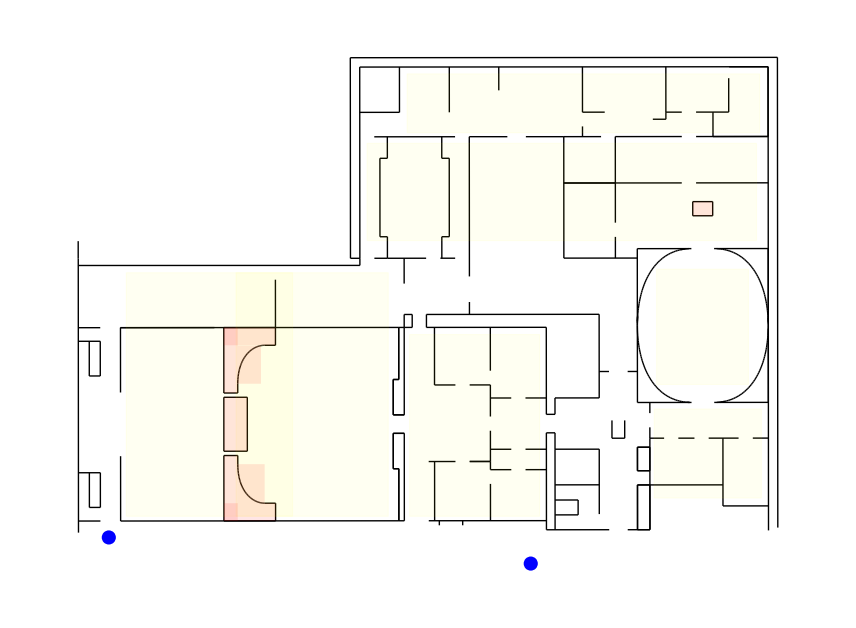

```mathematica
(*Agent Areas*)
(*xmin, ymin, xmax, ymax*)
agentAreas={
{{-43.52,-31.00},{-20.00,3.50}},
{{-28.00,-31.00},{-6.46,3.50}},
{{-3.45,-31.00},{14.96,-5.26}},
{{31.16,-28.42},{46.33,-15.8}},
{{31.51,-12.33},{44.50,4.00}},
{{-9.47,8.05},{45.64,21.83}},
{{-3.8,23.33},{46.1,31.67}}
};
agentTargets={(*Left exit, Right two exit mean*)
{-46.,-34.},{13.7,-37.7}};
(*Filled region, forbidding agent placement*)
filledObs={
{145,147},{144,155},{147,149},
{372,370},
{363,361},{309,358},{359,361},
{554,434}
};
filling[e1_,e2_]:=Module[
{p={Part[v4,e1+1],Part[v4,e2+1]}},
{
{Min@@First/@p,Min@@Last/@p},
{Max@@First/@p,Max@@Last/@p}
}];
agtConfInfo ={
{First@agentAreas, First@agentTargets, Area[Rectangle@@First@agentAreas]},
{#, Last@agentTargets,Area[Rectangle@@#]}&/@Rest@agentAreas
};

Graphics[
{Line@indexEdgeToLine[vLatest,eLatest],
{EdgeForm[Dotted],Yellow,Opacity[0.05],Rectangle@@@agentAreas},
{Red,Opacity[0.1],Rectangle@@@filling@@@filledObs},
{Blue,Disk/@agentTargets}
}]
```

## Tools for designing

```mathematica
DynamicModule[{queryX,queryY},
Grid[
{
{Slider[Dynamic[queryX],{-50,50}],Dynamic[queryX]},
{Slider[Dynamic[queryY],{-40,40}], Dynamic[queryY]},
{Graphics[{
Line@indexEdgeToLine[vLatest,eLatest],Disk[Dynamic[{queryX,queryY}],0.2]
},Frame->True,ImageSize->Large]}
}
]
]
```

```mathematica
_□
```

_□

```mathematica
DynamicModule[
{da,db,dc,dd,a,b,c,d},
Grid[
{
{Slider[Dynamic[a],{-50,50}],Dynamic[a]},
{Slider[Dynamic[b],{-40,40}],Dynamic[b]},
{Slider[Dynamic[c],{-50,50}],Dynamic[c]},
{Slider[Dynamic[d],{-40,40}],Dynamic[d]},
{Graphics[{
Line@indexEdgeToLine[vLatest,eLatest],
Disk[Dynamic[{a,b}]],
Disk[Dynamic[{c,d}]]
},Frame->True,ImageSize->Large]},
{Dynamic@Text@getVertsByRegion[a,c,b,d]}
}
]
]
```

## Real Challenge! Obstacle Moving!

```mathematica
getVertsByRegion[x1_,x2_,y1_,y2_]:=DynamicModule[
{regTest},
regTest[x_,y_]:=And[x1<x<x2,y1<y<y2];
#-1&/@Flatten@Position[regTest@@@vLatest,True]
];

updateVerts[cur_,{ori_,ref_},sVertL_,vertL_]:=Module[
{xy,diff,update},
diff=cur-ref;
xy=ori/.<|
0->Function[{x,y},{x+diff,y}],
1->Function[{x,y},{x,y+diff}]
|>;
update[v_,{vIdx_}]:=If[MemberQ[sVertL,vIdx-1],xy@@v,v];
MapIndexed[update,vertL]
];

notateComponent:=Module[
{arrow,notate},
arrow[0,c_,r1_,r2_,y_]:={Darker@Green,Arrow[{{c+1,y},{r2,y}}],Arrow[{{c-1,y},{r1,y}}]};
arrow[1,c_,r1_,r2_,x_]:={Darker@Green,Arrow[{{x,c+1},{x,r2}}],Arrow[{{x,c-1},{x,r1}}]};
notate[{0,x_,y_},{idx_}]:={Text[Style[idx,Tiny],{x,y}],Circle[{x,y},0.7]};
notate[{1,y_,x_},{idx_}]:={Text[Style[idx,Tiny],{x,y}],Circle[{x,y},0.7]};
{MapIndexed[notate,Part[#,{1,2,5}]&/@refPoints],
{Arrowheads[Tiny],arrow@@@refPoints}}
];

obsMutation[refp_,sVertL_]:=
DynamicModule[{cur,v},
cur=refp[[2]];
v:=updateVerts[Dynamic[cur],refp,sVertL,vLatest];
Grid[{
{Slider[Dynamic[cur],{-50,50},
ImageSize->Large],Dynamic[cur]},
{Graphics[
{Line@indexEdgeToLine[v,eLatest],
notateComponent
},
ImageSize->Large],Text["Placeholder"]}
}]
];
```

```mathematica
refPoints={
{0,-28.11,-42.4,-11.2,-8.00},
{0,-28.11,-47.4,-8.2,-18.00},
{0,-28.11,-42.4,-11.2,-27.20},
{0,8.00,5.6,10.2,-6.52},
{1,-12.25,-14.5,-6.7,2.06},
{0,8.00,5.6,10.2,-29.14},
{1,-23.00,-27.8,-20.7,2.06},
{0,26.07,19.0,24.7,-16.70},
{1,-18.70,-19.8,-16.6,24.07},
{1,-19.85,-24.4,-18.5,37.87},
{0,2.10,-2,10,28.5},
{0,9.16,-2,10,31.3},
{0,26.65,18,29,30.0},
{1,21.02,11,22,-2.5},
{0,3.26,1.0,6.8,15.0},
{0,18.30,13.9,22.4,15.0},
{0,25.61,23.24,34.6,19.0},
{1,16.27,12.0,17.1,30.0},
{1,-10.58,-2.5,-13.8,26.07},
{0,41.60,40.0,45.0,30.0},
{0,-22,-42.45,-5.8,-1},
{0,37.9,28,45,15.0},
{1,12.6,9.2,21.0,34.5},
{1,22.8,5.6,22.8,11.6}
};
selVerts={
{144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198},
{370,371,372,373},
{309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363},
{496,497,498,505,506,507,440,441,438},
{497,498,499,506,507,440,441,438,439},
{453,455,456,457,458,459,461,465,508,511,509,466},
{453,454,455,456,457,458,459,460,461,465,508,510,511,524},
{374,375,376,377},
{374,375,376,377},
{444,445,447,448,449,450,451,452,522,525},
{396,397},
{392,393},
{394,395,398,399,400,406,407,408,409,410},
{424,425,426,427,428,429,480,481},
{421,422,423,424,425,426,481,483,484,488,489,490,556},
{416,486,487,557},
{414,415,479},
{415,416,418,419,420,553,414,475,476,477,543,544},
{501,502,503,504},
{411,544,545,546,547},
{471,552},
{433,434,554,555},
{433,434,554,555},
{478,482,556,557}
};
obsMutation[refPoints[[#]][[{1,2}]],selVerts[[#]]]&@24
```

## Some Examples of Current Form

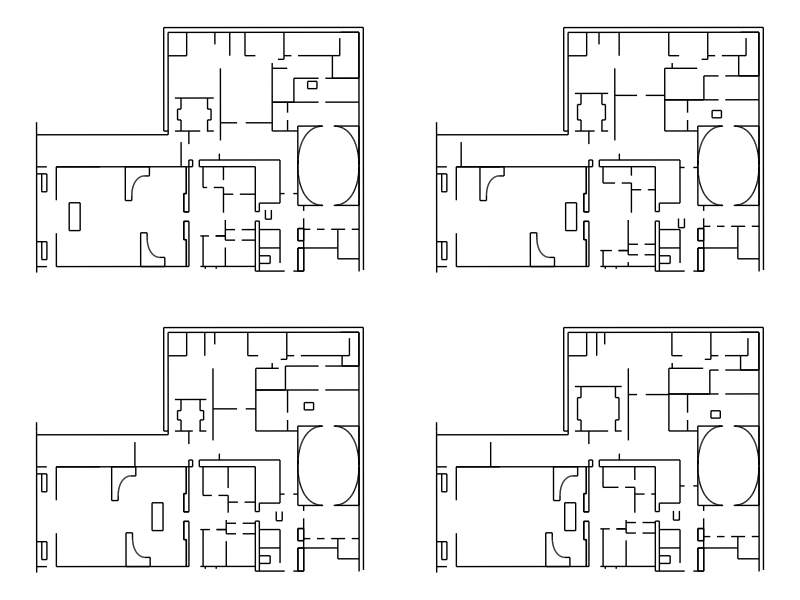

```mathematica
randState:=RandomReal[{},24]
randMap[state_]:=Module[
{ori,refPs,stPs,endPs,curPs,update,flist},
ori=refPoints[[All,1]];
refPs=refPoints[[All,2]];
stPs=refPoints[[All,3]];
endPs=refPoints[[All,4]];
curPs=state*(endPs-stPs)+stPs;
update[v_,{st_, o_,r_,sv_}]:=updateVerts[st,{o,r},sv,v];
flist=Transpose@{curPs,ori,refPs,selVerts};
Fold[update,vLatest,flist]
]
Grid[{
{showGraph [randMap[randState],eLatest],
showGraph [randMap[randState],eLatest]},
{showGraph [randMap[randState],eLatest],
showGraph [randMap[randState],eLatest]}
}]
```

## Export Data

```mathematica
Export["Metropolitan.json",
{
"vertexes"->Flatten[vLatest],
"edges"->Flatten[eLatest],
"filledObs"->Flatten[filledObs],
"refPoints"->Flatten[refPoints],
"selectedVertices"->selVerts,
"agentRegions"->Flatten[agtConfInfo]
}
]
```

Metropolitan.json